```mathematica
ClearAll["Global`*"];
```

```mathematica
ϵ=10^(-3);znak=3;

X0={-1,-2};α=1;
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2
(*X0={0,2 Sqrt[5]};f[{x_,y_}]=8x^2+5y^2-4x y+8Sqrt[5](x+2y)+64;(*X0={0,2 Sqrt[5]};X0={-Sqrt[5],0};*)*)
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
Hesse[{x1_,y1_}]:=D[f[{x,y}],{{x,y},2}]/.{x->x1,y->y1};
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
X=X0;
P={0,0};
points={X0};
norm={NormGradF[X0]};
ωArray={antiGradF[X0]};
fValues={f[X0]};
κArray={1};

H=Hesse[X];
κ=1;
w=0.3;
e={{1,0},{0,1}};
symi=0;i=0;
ifunk={0};


While[norm[[-1]]≥ϵ,
i=0;
H=Hesse[X];i+=9;
While[PositiveDefiniteMatrixQ[H]==False,H+=10*e;];
P=LinearSolve[Hesse[X],antiGradF[X]];
(*κArray=Append[κArray,NArgMin[f[X+y P],y,StepMonitor:>i++]];κ=κArray[[-1]];(*исчерпывающий спуск*)*)
κ=1;
      (*While[fValues[[-1]]-f[X+κ*P]<w*κ*ωArray[[-1]].P,i++;κ*=0.5;];  i++;(*модификация метода Ньютона дроблением шага*)*)
X+=κ*P;  
points=Append[points,X];
fValues=Append[fValues,f[X]];
ωArray=Append[ωArray,antiGradF[X]];i+=3;
κArray=Append[κArray,κ];
norm=Append[norm,NormGradF[X]];          
symi+=i;        ifunk=Append[ifunk,i];                 
];"Результат получен за "<>ToString[Length[points]-1]<> " итер. Точка минимума X = "<>ToString[SetAccuracy[X,znak]]<>". Функция f(x) в алгоритме была вычислена "<>ToString[symi]<>" раз."
SetAccuracy[f[X],znak]" - минимум функции f(X)"
```

Результат получен за 5 итер. Точка минимума X = {1.0, 1.0}. Функция f(x) в алгоритме была вычислена 45 раз.

0.  - минимум функции f(X)

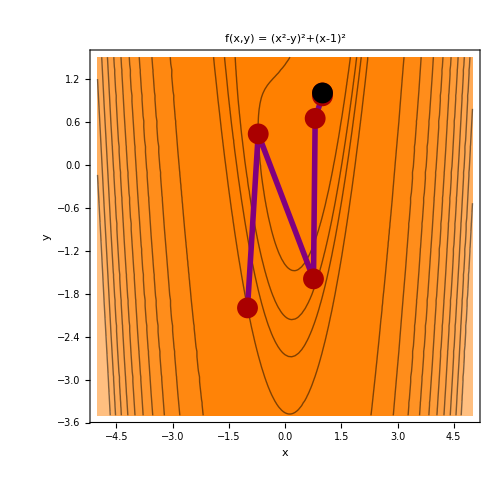

```mathematica
CP0={-5,-3.5}; CP1={5,1.5};
(*CP0={-5,-3.5}; CP1={5,1.5};(*Функция Розенброка при лямбда = 1,50,1000*)*)
(*CP0={-5,-5}; CP1={5,5}; Квадратичная функция с нач приближ X0={0,2 Sqrt[5]};*)
(*CP0={-5,-5}; CP1={1,1}; Квадратичная функция с нач приближ X0={-Sqrt[5],0};*)
 a:=Length[points]-1;b:=Length[points];
ContourPlot[f[{x,y}],{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;2]]~Join~{fValues[[a]],fValues[[b]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Line[points],Darker[Red],PointSize[0.03],Point[points],Black,Point[points[[Length[points]]]]}]
```

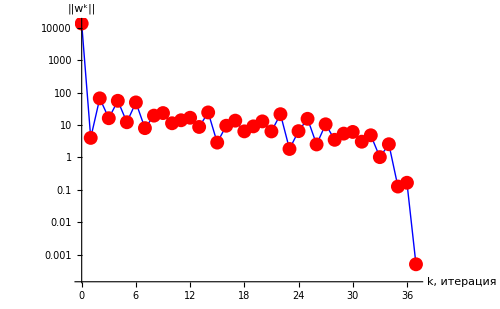

```mathematica
ListLogPlot[norm,DataRange->{0,Length[points]-1},PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"},ImageSize->500,Joined->True,Mesh->Full,MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
gridLabel={"k","X^k","f(X^k)","||w^k||","κ"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
For[i=1,i≤Length[points],i++,gridData[[i,2]]="("<>ToString[SetAccuracy[points[[i,1]],znak]]<>", "<>ToString[SetAccuracy[points[[i,2]],znak]]<>")"]
gridData[[All,3]]=SetAccuracy[fValues,znak];
gridData[[All,4]]=SetAccuracy[norm,znak];
gridData[[All,5]]=SetAccuracy[κArray,znak];
gridData={gridLabel}~Join~gridData;Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

k | X^k | f(X^k) | ||w^k|| | κ
0 | (-1.00, -2.00) | 9004. | 13400. | 1.
1 | (-1.0, 1.0) | 4. | 0``-5.033616737065403 | 1.
2 | (-0.87, 0.75) | 3.76 | 66.2 | 0.06
3 | (-0.82, 0.66) | 3.31 | 16.17 | 1.
4 | (-0.70, 0.47) | 3.12 | 55.64 | 0.5
5 | (-0.65, 0.41) | 2.72 | 12.15 | 1.
6 | (-0.52, 0.26) | 2.59 | 49.59 | 0.5
7 | (-0.48, 0.23) | 2.19 | 8. | 1.
8 | (-0.41, 0.16) | 2.02 | 19.42 | 0.25
9 | (-0.31, 0.09) | 1.8 | 23.29 | 1.
10 | (-0.24, 0.05) | 1.56 | 11.3 | 1.
11 | (-0.18, 0.03) | 1.43 | 13.99 | 0.5
12 | (-0.09,      -3
0. 10) | 1.25 | 16.71 | 1.
13 | (-0.03,       -2
-0. 10) | 1.07 | 8.69 | 1.
14 | (0.08,       -2
-0. 10) | 0.99 | 24.37 | 1.
15 | (0.12, 0.01) | 0.78 | 2.86 | 1.
16 | (0.18, 0.03) | 0.69 | 9.48 | 0.25
17 | (0.26, 0.06) | 0.59 | 13.6 | 1.
18 | (0.31, 0.1) | 0.48 | 6.36 | 1.
19 | (0.36, 0.13) | 0.42 | 9.06 | 0.5
20 | (0.44, 0.18) | 0.35 | 12.9 | 1.
21 | (0.49, 0.23) | 0.27 | 6.33 | 1.
22 | (0.57, 0.32) | 0.24 | 21.51 | 1.
23 | (0.60, 0.36) | 0.16 | 1.82 | 1.
24 | (0.64, 0.41) | 0.14 | 6.46 | 0.25
25 | (0.71, 0.49) | 0.11 | 15.5 | 1.
26 | (0.73, 0.54) | 0.07 | 2.51 | 1.
27 | (0.78, 0.61) | 0.05 | 10.49 | 0.5
28 | (0.82, 0.67) | 0.03 | 3.49 | 1.
29 | (0.85, 0.72) | 0.03 | 5.42 | 0.5
30 | (0.89, 0.78) | 0.02 | 6.1 | 1.
31 | (0.91, 0.84) | 0.008 | 3.05 | 1.
32 | (0.95, 0.90) | 0.004 | 4.81 | 1.
33 | (0.96, 0.93) | 0.001 | 1.02 | 1.
34 | (0.99, 0.98) | 0. | 2.55 | 1.
35 | (0.99, 0.99) | 0. | 0.13 | 1.
36 | (1.0, 1.0) | 0. | 0.17 | 1.
37 | (1.0, 1.0) | 0. | 0. | 1.